```mathematica
On[Assert]
Clear["`*"]
```

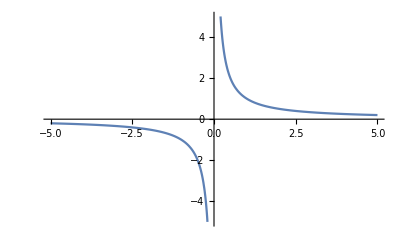

```mathematica
Plot[1/x,{x,-5,5}, PlotRange->{{-5,5},{-5,5}}]
```

```mathematica
d[p1_,p2_]:=Sqrt[(p1[[1]]-p2[[1]])^2+(p1[[2]]-p2[[2]])^2]
```

```mathematica
f[x_]:=1/x
```

```mathematica
cLine=k x+lB;
```

```mathematica
cLineAssumptions={k>0,lB∈Reals};
```

```mathematica
cLineF[x_]=cLine;
```

```mathematica
solved=x/.Solve[cLine==f[x],x,Assumptions->cLineAssumptions]//Simplify//Flatten
```

{-(lB+√(4 k+lB^2))/(2 k),(-lB+√(4 k+lB^2))/(2 k)}

```mathematica
{Sign[solved[[1]]]//Simplify[#,Assumptions->cLineAssumptions]&,
Sign[solved[[2]]]//Simplify[#,Assumptions->cLineAssumptions]&}
```

{-1,1}

```mathematica
pP1={solved[[1]],f[solved[[1]]]};
pP2={solved[[2]],f[solved[[2]]]};
```

```mathematica
center=Midpoint[{pP1,pP2}]
```

{-lB/(2 k),lB/2}

```mathematica
Assert[Simplify[d[center,pP1]==d[center,pP2]]]
```

```mathematica
a=d[center,pP1]//Simplify
```

1/2 √(((1+k^2) (4 k+lB^2))/k^2)

```mathematica
d[{m,cLineF[m]},center]==c
```

√((lB/(2 k)+m)^2+(lB/2+k m)^2)==c

```mathematica
pF={m,n}/.Solve[{d[{m,n},center]==c,cLineF[m]==n},{m,n},Assumptions->cLineAssumptions~Join~{m>0,n>0,c>0}]//Flatten//Normal//Simplify
```

{c/(√(1+k^2))-lB/(2 k),(c k)/(√(1+k^2))+lB/2}

```mathematica
pF2=pF;
```

```mathematica
pF1={m,n}/.Solve[Midpoint[{{m,n},pF2}]==center,{m,n}]//Flatten
```

{(-2 c k-√(1+k^2) lB)/(2 k √(1+k^2)),(-2 c k+√(1+k^2) lB)/(2 √(1+k^2))}

```mathematica
Assert[Midpoint[{pF1,pF2}]==center]
```

```mathematica
l=d[{x,f[x]},pF1]-d[{x,f[x]},pF2]//Abs
```

Abs[-√((-(c k)/(√(1+k^2))-lB/2+1/x)^2+(-c/(√(1+k^2))+lB/(2 k)+x)^2)+√((-(-2 c k+√(1+k^2) lB)/(2 √(1+k^2))+1/x)^2+(-(-2 c k-√(1+k^2) lB)/(2 k √(1+k^2))+x)^2)]

```mathematica
Solve[{l==2a,a^2+b^2==c^2},{b,c},Assumptions->cLineAssumptions~Join~{m>0,n>0,c>0,b>0}]
```

$Aborted